-Graphics-

# Speeding up Mathematica code

## I re-wrote my program with functional constructs, and it still runs slowly - Help!

## David Bailey http://dbaileyconsultancy.co.uk

## Introduction

While Mathematica simplifies the writing of complex code in many ways, producing high performance code can be challenging. While the following examples are simple, they illustrate problems that often occur in more complicated contexts, and some novel solutions. Note that timings will vary with the type of processor, and that problems may need to be scaled up a little to provide sensible timings on fast machines. I will cover the following topics:

• Some generalisations about software performance.

• Two specific examples of poor Mathematica performance (and how to fix them).

• A simple tool to explore program performance.

• A discussion of functional programming – why does it often deliver performance gains in Mathematics.

• A discussion of packed and sparse arrays.

• A way to combine elegant code with efficiency – macros.

• An example of poor graphics performance.

• A brief discussion of other wsays to speed up Mathematica code

## Lessons from old fashioned programming

• Do I really need to make my code more efficient?

• Programs spend almost all their time in a few critical areas – often not the areas that you expect.

• Scale your calculation (or break it into sections), so that you can explore code that runs for 10-30 seconds. You will never optimise a program that takes 3 hours each time it is run!

• Is the algorithm at fault?

For example, there are various algorithms that can speed up a digital Fourier transform, for particular lengths. The best known such algorithm is the FFT, which works on lengths which are a power of 2, and reduces the cost from O[N^2] to O[N Log[N]]. Mathematica obviously recognises such special cases, so transforming a slightly longer sequence may actually take less time!

```mathematica
vec=RandomReal[1.0,1000001];
Do[Fourier[vec],{20}]//DB˘Timing
```

{"58.43" secs,Null}

```mathematica
len=2^20
vec=RandomReal[1.0,len];
Do[Fourier[vec],{20}]//DB˘Timing
```

1048576

{"10.94" secs,Null}

• Make sure you have adequate test results – otherwise you may speed up your code by simply breaking it!

• Seed all random number generation so you get identical results from run to run (also vital when you are debugging code).

## Timing tools

The following tool makes it easy to time the execution of a task, inserting timing probes within the code, that can also show intermediate results. Timing˘Print uses AbsoluteTime rather than Time. It could obviously be converted to use Time, however:

• It seems reasonable to assume that timing experiments will not be done with other CPU intensive tasks running in the background!

• AbsoluteTime measures wall clock time and captures such things as time spent in the FrontEnd, or in Java (some built-in functions such as Import use Java internally).

• It is possible to split a task across more than one kernel. Potentially, this makes sense in a multi-core environment, although parallel programming is not explored in this paper. In this context, only AbsoluteTime makes sense.

• Ultimately it is wall clock time that is important – how long do I need to wait for my answer!

```mathematica
SetOptions[SelectedNotebook[],CellProlog:>(timing˘start=AbsoluteTime[])];
SetAttributes[Timing˘Print,HoldFirst];
Options[Timing˘Print]={"FrontEndWait"->False};
Timing˘Print[x_,OptionsPattern[Timing˘Print]]:=Module[{ans=x,ll},
If[OptionValue["FrontEndWait"],
LinkWrite[$ParentLink,CellInformation[SelectedNotebook[]]];
LinkRead[$ParentLink];
];
ll={};
If[True,ll={"(",NumberForm[Chop[AbsoluteTime[]-timing˘start,0.01],{10,2}]," secs): "}];
If[ListQ[ans] && Length[ans]>0,
ll=Append[ll,If[Developer`PackedArrayQ[ans],
" (Packed array)",
If[Developer`PackedArrayQ[Developer`ToPackedArray[ans]]," (Packable unpacked array )"," (Unpackable array)"]
]<>ToString[Dimensions[ans]]<>" "];
];
ll=Append[ll,Defer[Short[x]]];
If[Unevaluated[x]=!=ans,ll=Join[ll,{"=",Short[ans]}]];
   CellPrint[Cell[BoxData[
            ToBoxes[SequenceForm[Sequence@@ll]]
            ],
            Background->Cyan,"Print"]];
   If[StringQ[Unevaluated[x]],Null,ans]
   ];
```

This is a utility function to pick present the output from Timing in a more readable form.

```mathematica
SetAttributes[DB˘Timing,HoldAll];
DB˘Timing[x_]:=Module[{ans=Timing[x]},
{Style[StringForm["`` secs",NumberForm[ans[[1]],{5,2}]],FontColor->Red,FontWeight->Bold],ans[[2]]}
];
```

• Timing˘Print prints its argument before and after evaluation, returning the final result unless the unevaluated input was a string.

• Because the packing of arrays is so important for performance, Timing˘Print prints the packing status of any list. This may consume a little time, so subsequent timing points could be affected.

• Using the option “FrontEndWait”->True forces a wait until the FrontEnd has finished any rendering operation – very useful for accounting for the time used in graphics operations.

• If you insert Timing˘Print in very tight loops, or you use it to print out large objects, the time spent within Timing˘Print itself may distort the results.

• A modern PC is a complex environment, and any form of timing will return results that vary somewhat from run to run.

## A first example

### The problem

This program, which is almost ridiculously simple, reads 200000 lines of comma-separated 8-column data from a file, and sums the columns. The code is deliberately fairly naive, but remember that in more complicated cases, it may be hard to avoid procedural code.

```mathematica
(
data=Import["C:\\maths\\conference_2010\\Data1.csv"];
totals=Table[0,{8}];
Do[
totals=totals+data[[m]],
{m,Length[data]}];totals
 )//DB˘Timing
```

{"30.72" secs,{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}}

### Switch to functional programming

Everyone knows that using functional programming is the way to speed up Mathematica code:

```mathematica
(data=Import["C:\\maths\\conference_2010\\Data1.csv"];
totals=Total[data];totals )//DB˘Timing
```

{"30.71" secs,{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}}

### Think again!

That was no real difference – what went wrong? We need to find out where the CPU time is spent – not just guess! We also need some better tools.

```mathematica
data=Import["C:\\maths\\conference_2010\\Data1.csv"];
Timing˘Print["Data read in"];
totals=Table[0,{8}];
Timing˘Print["Result array initialised"];
Do[
totals=totals+data[[m]],
{m,Length[data]}];
Timing˘Print["Totals calculated"];
totals
```

(29.21 secs): Data read in

(29.38 secs): Result array initialised

(32.29 secs): Totals calculated

{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}

• Thus most of the time was spent in the Import function!

• Had we used a double loop for the calculation (Fortran 77 style), the Import operation would have only used about 2/3 of the CPU, so the switch to functional code would have been a bit more impressive.

• The Import function is a wrapper for a whole suite of functions – some of which have been highly optimised, and others less so. Don’t assume that just because the work is done entirely inside one call to a built-in function, that you can’t do better.

### Deal with the real inefficiency

The Import of CSV files is not very efficient, and it is easy to improve the performance:

```mathematica
data=Partition[ReadList["C:\\maths\\conference_2010\\Data1.csv",Real,RecordSeparators->{"\n"," ","\t",","}],8];
Timing˘Print["Data read in"];
totals=Table[0,{8}];
Timing˘Print["Result array initialised"];
Do[
totals=totals+data[[m]],
{m,Length[data]}];
Timing˘Print["Totals calculated"];
totals
```

(5.37 secs): Data read in

(5.56 secs): Result array initialised

(8.46 secs): Totals calculated

{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}

### Use functional programming for a final polish:

```mathematica
data=Partition[ReadList["C:\\maths\\conference_2010\\Data1.csv",Real,RecordSeparators->{"\n"," ","\t",","}],8];
Timing˘Print["Data read in"];
totals=Total[data];
Timing˘Print["Totals calculated"];
totals
```

(5.76 secs): Data read in

(8.33 secs): Totals calculated

{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}

### Frequently we can do even better!

In many situations, it is necessary to read the same data many times – the data changes less frequently than the program. In this case, we can save the data in binary format and restore it with Get. This is extraordinarily efficient!

```mathematica
DumpSave["c:\\ttt\\hope.mx",data];
```

```mathematica
Quit[];
```

```mathematica
Print["Back"]
```

Back

```mathematica
Get["c:\\ttt\\hope.mx"];
Timing˘Print["Data read in"];
Dimensions[data]
```

(1.05 secs): Data read in

{200000,8}

• Note that mx files are tied to the version of Mathematica, so a prudent programmer will use Catch to trap the error if Get fails, and read the data in via a slower mechanism, possibly recreating the mx file again for future use.

• DumpSave can store several items at once, so a really prudent programmer will store the date/time last modified of the CSV file inside the mx file. If this doesn’t match when the file is read back, the original data has changed, and it is necessary to read it the slower way, and re-create the mx file.

## How to be really inefficient

### The problem

We want to study the convergence of successive iterates of the Newton Raphson approximation to the solution of an equation

```mathematica
func=(1+3x^2+5x^3)/(1+x^5/2);
```

Find x such that func==3

```mathematica
dfunc=D[func,x]//Simplify
```

-(2 x (-12-30 x+5 x^3+9 x^5+10 x^6))/((2+x^5)^2)

```mathematica
(A-func)/dfunc//Simplify
```

-((2+x^5) (-2 (1+3 x^2+5 x^3)+A (2+x^5)))/(2 x (-12-30 x+5 x^3+9 x^5+10 x^6))

### Exact answer

```mathematica
FindRoot[func==3,{x,1.0}]//InputForm
```

{x -> 0.5945666836622415}

### Calculate successive iterates

```mathematica
NR˘Approx[x_,n_,A_]:=Module[{xn=x},
Do[
xn=xn-((2+xn^5) (-2 (1+3 xn^2+5 xn^3)+A (2+xn^5)))/(2 xn (-12-30 xn+5 xn^3+9 xn^5+10 xn^6)),
{n}
];
xn
];
```

Fourteen seconds is an absurd amount of time for this calculation!

```mathematica
Table[NR˘Approx[1,n,3]-0.5945666836622415,{n,1,7}]//DB˘Timing
```

{"14.95" secs,{-0.344567,0.3712,-0.200422,0.0702573,0.0026331,5.50194×10^-6,2.43305×10^-11}}

This takes about 300 seconds – clearly something is badly wrong.

```mathematica
NR˘Approx[1,8,3];Timing˘Print["Done!"]
```

(299.88 secs): Done!

### Try functional programming

Once again, we try to improve the performance by using functional programming.

```mathematica
NR˘Approx[x_,n_,A_]:=Nest[(#-((2+#^5) (-2 (1+3 #^2+5 #^3)+A (2+#^5)))/(2 # (-12-30 #+5 #^3+9 #^5+10 #^6)))&,x,n]
```

```mathematica
NR˘Approx[1,8,3];Timing˘Print["Done!"]
```

(302.10 secs): Done!

### Where did the time go?

This calculation is extraordinarily simple – the loop only goes round a small number of times, so how can it possibly be so slow! We need to find out what is happening!

When Timing˘Print is applied to something that can be evaluated, it prints it before and after evaluation, and returns its value as the final result (unlike, say Print). This means that it can be inserted into code with a minimum of rearrangement.

```mathematica
NR˘Approx[x_,n_,A_]:=Module[{xn=x},
Do[
xn=xn-((2+xn^5) (-2 (1+3 xn^2+5 xn^3)+A (2+xn^5)))/(2 xn (-12-30 xn+5 xn^3+9 xn^5+10 xn^6)),
{n}
];
Timing˘Print@xn
];
```

```mathematica
NR˘Approx[1,4,3]-0.5945666836622415
```

(0.01 secs): xn$2081=(9266763705317824853535220651927361634«538»9882028752592443304197607965172034627)/(1393867200257996309130409748889556570«539»0491320974616512905166007718304022528)

0.0702573

It is now obvious that the problem was that the calculation was inadvertently being performed using Rational arithmetic! I made this mistake myself in a different calculation that ended in a plot – so just as here, the error was not instantly obvious. With a trivial change, a 300 second calculation takes a barely measurable amount of time!

```mathematica
NR˘Approx[1.0,8,3];Timing˘Print["Done!"]
```

(0.01 secs): xn$2084=0.594567

(0.05 secs): Done!

Mistakes of this sort often happen in complicated contexts, buried in code. As you can see, they can easily swamp all other performance considerations.

## Functional programming

While it is true that functional programming often provide a substantial speed up within Mathematica, it is important to understand why it does this.

Modern Fortran enables users to operate on whole arrays without writing an explicit DO-loop. This is similar to some of Mathematica’s functional programming constructs, yet these Fortran constructs offer little, if any speed advantage over writing one or more DO-loops in full!

Functional programming provides a big gain in Mathematica because individual program steps carry a large, inevitable overhead. Consider a step such as:

```mathematica
j=j+1
```

or

```mathematica
j++
```

(These statements are valid in both C and Mathematica)

In a fully compiled language, these statements would compile to 1 to 3 machine instructions (depending on the CPU architecture). However Mathematica has to do many additional things, such as:

• Check if j has a value, and if so what type it is - switching to different code to handle each case (integer, real, symbolic, etc.).

• Check for overflow – because machine integers must smoothly overflow into software (infinite precision) integers.

• Cater for the possibility that Increment has been modified by the user! (If you execute the following code, kill the kernel afterwards, to avoid confusion!)

```mathematica
Unprotect[Increment];
Increment[x_]:=x+2
```

```mathematica
x=5;
```

```mathematica
x++
```

7

Fortran code normally carries out none of these steps – except perhaps the integer overflow check if checking is enabled by the compiler (generating an error, not switching to software integers!).

Thus, a convenient way to understand the gain from functional programming, is to recognise that it reduces the number of steps required to complete a task:

```mathematica
vec=RandomReal[1.0,5000000];
```

Typical example of efficient functional programming – vec and Sin are only accessed once.

```mathematica
res=Map[Sin,vec];//DB˘Timing
```

{"1.65" secs,Null}

Here vec, j, and Sin will each be accessed 5 million times

```mathematica
res=ConstantArray[0.0,5000000];
```

```mathematica
Do[res[[j]]=Sin[vec[[j]]],{j,5000000}];//DB˘Timing
```

{"33.28" secs,Null}

A significant part of the speed comes from the combination of FP and packed arrays.

```mathematica
vec[[1]]=0;
Map[Sin,vec];//DB˘Timing
```

{"5.38" secs,Null}

If the function being mapped, is itself quite complicated, then the reduction in steps (and hence performance improvement) associated with FP can be much smaller. Note that these tests are being done on 1/10 as many points:

```mathematica
sin[x_]:=x-x^3/6+x^5/120;
```

```mathematica
vec=RandomReal[1.0,500000]; (* reduced vector size to get convenient timings *)
res=ConstantArray[0.0,500000];
```

```mathematica
res=Map[sin,vec];//DB˘Timing
```

{"9.84" secs,Null}

```mathematica
res=Map[(#-#^3/6+#^5/120)&,vec];//DB˘Timing
```

{"0.39" secs,Null}

```mathematica
Do[res[[j]]=sin[vec[[j]]],{j,500000}];//DB˘Timing
```

{"12.91" secs,Null}

• The results here are interesting. Map outperforms an explicit do-loop, but not by very much. Calling the function, which contains several arithmetic steps, means that the percentage reduction in overhead is not too great.

• The remarkable result, however, is that Map using the pure function performs so well. I speculate that Mathematica attempts to compile the pure function (perhaps because it is a simple mathematical expression), and uses that for the calculation.

• Arguably the real conclusion of this section, is that timings can be a little unexpected, and if you are looking at the rate-critical step of your program, it is worth doing a little experimentation to determine what performs best.

## Arrays – packed, sparse, and vanilla

### Packed arrays

Most programs that need to be efficient, need to process large quantities of data. Therefore efficient array manipulation is vital. We return briefly to the initial example:

```mathematica
data=Import["C:\\maths\\conference_2010\\Data1.csv"];
Timing˘Print[data];
```

(29.30 secs):  (Packable unpacked array ){200000, 8} data={{0.752939,0.715869,1.14451,1.03694,1.25999,0.674417,1.46465,0.519579},«199998»,{1.35372,«6»,1.01113}}

• The using Timing˘Print on an array, it is possible to get a glimpse of what it contains, and establish if it was packed, and if it could have been packed – information that is highly relevant to performance.

• Timing˘Print uses Short to avoid generating excessive output, but even so, it is an expensive operation when used on large objects, so we substitute strings to explore the cost of explicitly packing this array:

```mathematica
data=Import["C:\\maths\\conference_2010\\Data1.csv"];
Timing˘Print["Before packing"];
data=Developer`ToPackedArray[data];
Timing˘Print["Done"];
```

(28.83 secs): Before packing

(29.16 secs): Done

• Thus explicit packing of arrays is almost always beneficial because it is so fast, and note that it is not an error to pack an array that is already packed. Compare the time required to toal the raw data with that required to total the packed data!

```mathematica
data=Import["C:\\maths\\conference_2010\\Data1.csv"];
Total[data]//DB˘Timing
```

{"2.31" secs,{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}}

```mathematica
data=Developer`ToPackedArray[data];
Total[data]//DB˘Timing
```

{"0.05" secs,{199951.,199884.,199768.,200020.,200068.,199879.,200071.,199995.}}

• Observe that the Total operation executed much faster on the packed array – although these times are too short for accurate use.

• The packing of arrays is often spoiled by the occasional integer scattered among real data:

```mathematica
data[[3,3]]=0;
data=Developer`ToPackedArray[data];
Total[data]//DB˘Timing
```

{"1.17" secs,{99984.1,100004.,99879.5,99858.9,99895.9,100004.,99966.4,100050.}}

• If in doubt, use N to force all data to real type – it is pretty fast, so the cost is usually worth it, or use a second, type argument to ToPackedArray.

```mathematica
data=N[data];//DB˘Timing
```

{"0.32" secs,Null}

### Sparse arrays

Sparse arrays represent arrays that contain many zero entries (more generally, many elements with some particular default value). Here are a few examples to work with:

```mathematica
sa1=SparseArray[{{1}->10.,{50}->9.}] (* a sparse vector *)
```

SparseArray[<2>,{50}]

```mathematica
ByteCount[sa1]
```

808

```mathematica
sa2=SparseArray[{{1,1}->10.,{50,50}->9.}] (* a moderate sized sparse array *)
```

SparseArray[<2>,{50,50}]

```mathematica
sa3=SparseArray[{{1,1}->10.,{50,50}->9.},Automatic,NotAvailable] (* sparse array with a different sort of default element *)
```

SparseArray[<2>,{50,50},NotAvailable]

```mathematica
sa4=SparseArray[Table[{RandomInteger[{1,50000}],RandomInteger[{1,50000}]}->RandomReal[],{1000000}]]; (* 50000 x 50000 array with about 1000000 non-default entries *)
```

• The beauty of SparseArrays, is that most relevant built-in operations, such as Part, operate as though the array was completely fleshed out with default values. Some operations are quite clever, and manipulate the default value to avoid fleshing out the whole matrix:

```mathematica
sa2+1
```

SparseArray[<2>,{50,50},1.]

• Even so, for some uses of sparse arrays, this may not produce a useful result!

```mathematica
sa3+1
```

SparseArray[<2>,{50,50},1.+NotAvailable]

• The limits of the sparse array concept occur when Mathematica can’t figure out how to avoid processing the whole array. Compare these two operations:

```mathematica
foo[x_]:=(count++);
count=0;
Map[foo,sa4,{2}];//DB˘Timing
```

{"3.92" secs,Null}

```mathematica
MapIndexed[foo[#1]&,sa4,{2}];//DB˘Timing
```

SparseArray::ntb: Cannot convert the sparse array SparseArray[Automatic, {50000, 50000}, 0, « 1 »] to an ordinary array because the 2500000000 elements required exceeds the current size limit.

SystemException[SparseArrayNormalLimit,Normal[SparseArray[<999807>,{50000,50000}]]]

• Thus Map works with the sparse array concept, MapIndexed just tries to expand the array – a process that will either be expensive, or fail completely, as in this example.

• This shows that we really need a way to perform operations efficiently on sparse arrays when Mathematica wants to treat them as full arrays. One way is to convert a sparse array into a set of array rules:

```mathematica
ArrayRules[sa2]
```

{{1,1}→10.,{50,50}→9.,{_,_}→0}

• The conversion between a sparse array and the corresponding set or array rules, is pretty fast, and it is one way to continue to use a sparse data representation, even when some steps can’t use a SparseArray construct.

```mathematica
ArrayRules[sa4];//DB˘Timing
```

{"2.97" secs,Null}

### Exploring sparse arrays

Warning: The structure of sparse arrays might change in future versions, so don’t open them up without good reason, isolate and comment the relevant code so that it could be made version dependent if necessary.

The structure of sparse arrays is not completely opaque in the way that, for example, streams are opaque. They seem to built out of normal Mathematica primitives, and indeed the help for SparseArray suggests one way to dive under the hood!

First note that we can view the structure of sparse arrays using InputForm:

```mathematica
sa1//InputForm
```

SparseArray[Automatic, {50}, 0, {1, {{0, 2}, {{1}, {50}}}, {10., 9.}}]

```mathematica
sa2//InputForm
```

SparseArray[Automatic, {50, 50}, 0, {1, {{0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 
   1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 2}, {{1}, {50}}}, {10., 9.}}]

• For some operations, it is useful to extract the vector of non-default values, which can be found at position {4,3} in this structure:

```mathematica
break˘open[HoldPattern[SparseArray[x__]]]:=g[x];
```

```mathematica
Part[break˘open[sa2],4,3]
```

{10.,9.}

• The cost of obtaining the vector of values, is much less than would be the case using ArrayRules.

```mathematica
(tmp=Part[break˘open[sa4],4,3];)//DB˘Timing
```

{"0.00" secs,Null}

```mathematica
Dimensions[tmp]
```

{999807}

```mathematica
tmp[[1;;10]]
```

{0.109826,0.256595,0.16255,0.214687,0.10631,0.21347,0.422427,0.895494,0.307635,0.483507}

• It is also possible to change the non-default entries in the sparse array with modified data:

```mathematica
tmp=break˘open[sa2];
tmp[[4,3]]= -tmp[[4,3]];
res=SparseArray@@tmp
```

SparseArray[<2>,{50,50}]

```mathematica
res//Normal
```

{{-10.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9.}}

• These techniques are most useful when processing sparse arrays with large numbers of non-default entries – particularly in contexts other than Linear algebra. For example, the Labeled Array package, invented by Markus van Almsick, and used in Hans-Gerlach Woudboer’s Business Modeling software, uses large, high dimensional arrays containing data with missing entries, such as:

|  | Accounting | Facility | IT | OFC | SWB | Travel
Expense | Region | ⬚ |  |  |  |  | 
John | Region1 |  | 16.7101 | 1 | ⬚ | 4 | 10
David | Region1 |  | 22.658 | 1 | 1 | 7 | ⬚
Mary | Region1 |  | 14.7275 | 1 | 1 | 3 | 26
Fred | Region1 |  | 26.6232 | 1 | 1 | 9 | 5
Jill | Region2 |  | ⬚ | 1 | 1 | 3 | 23
Andrew | Region2 |  | 18.6928 | 1 | 1 | 5 | 6
Jane | Region2 |  | 24.6406 | ⬚ | 1 | ⬚ | 16
Ann | Region2 |  | 20.6754 | 1 | 1 | 6 | 16
Bill | Region2 |  | ⬚ | 1 | 1 | 4 | 24
Peter | Region2 |  | 12.7449 | 1 | 1 | 2 | ⬚

In these matrices, the default entry is NotAvailable, rather than zero.

## Macros in Mathematica

Many C and C++ programmers make extensive use of macros. These enable the programmer to write code that is changed even while it is being compiled. Frequently this is done to make code more efficient without making it obscure to read. For example, one might define a macro such as:

```mathematica
#define next_char() charpt++
```

This would mean that the programmer would write next_char(), but instead of this compiling into a function call, it would be replaced at compile time by the code "charpt++", which increments a pointer (usually one machine instruction).

C macros have a bad reputation (which lead to their exclusion from the Java language), because they can obscure code. Usually this is unintentional, but there is an international competition to produce the most obscure C code possible – usually achieved using macros. Here is an extreme example, which produces an approximation to the constant π:

```mathematica
#include <stdio.h>
#define _ F-->00 || F-OO--;
long F=00,OO=00;
main(){F_OO();printf("%1.3f\n", 4.*-F/OO/OO);}F_OO()
{
            _-_-_-_
       _-_-_-_-_-_-_-_-_
    _-_-_-_-_-_-_-_-_-_-_-_
  _-_-_-_-_-_-_-_-_-_-_-_-_-_
 _-_-_-_-_-_-_-_-_-_-_-_-_-_-_
 _-_-_-_-_-_-_-_-_-_-_-_-_-_-_
_-_-_-_-_-_-_-_-_-_-_-_-_-_-_-_
_-_-_-_-_-_-_-_-_-_-_-_-_-_-_-_
_-_-_-_-_-_-_-_-_-_-_-_-_-_-_-_
_-_-_-_-_-_-_-_-_-_-_-_-_-_-_-_
 _-_-_-_-_-_-_-_-_-_-_-_-_-_-_
 _-_-_-_-_-_-_-_-_-_-_-_-_-_-_
  _-_-_-_-_-_-_-_-_-_-_-_-_-_
    _-_-_-_-_-_-_-_-_-_-_-_
       _-_-_-_-_-_-_-_-_
            _-_-_-_
}
```

C macros operate before an expression is even parsed. The macros implemented here, operate after parsing – retaining most of their real value, without such an ability to confuse!

Mathematica does not contain a built-in macro capability, but it does permit the user to preprocess expressions as they are read in by assigning a suitable function to $Pre. However, I decided not to use this feature, because much of my code ends up in package files (.m), and if these are read by Get, $Pre is not used. This leaves two alternative ways to handle macros. One is to define a new operator – OverTilde[:=] – and use this instead of := where macro expansion is required, alternatively, we can overload SetDelayed to perform the necessary expansions. We use the latter approach here – neater, but maybe a little more dangerous!

The following implementation includes two types of macros – simple substitutional macros, and macros that execute at load time to achieve more complex results. The code is also subject to a final cleanup, to remove obvious examples of code that can be precomputed – such as 2^16 – such expressions can result from the expansion of macros, or be present in the source for reasons of clarity. Thus 2^16 makes more sense than 65536 in the context of Fourier transforms!

The code is written as a package, and could be transferred to a package file Macros.m if desired.

### Implementation

```mathematica
BeginPackage["Macros`"];
```

```mathematica
Define˘Macro::usage="Define˘Macro[patt,val] – Defines a macro that replaces patt with val before execution starts. Define˘Macro[symbol] – Defines an executable macro with the given head";
Macro˘Hold::usage="Executable macros often wrap their final answer in Macro˘Hold to prevent evaluation until after re-insertion into the code.";
```

```mathematica
Begin["`Private`"];
```

```mathematica
macro˘substitutions=Hold[];
executable˘macros={};
expanding˘macros=False;
SetAttributes[md˘hold,HoldAll];
SetAttributes[Macro˘Hold,HoldAll];
SetAttributes[macro˘expand,HoldAll];
(*SetAttributes[passivate,HoldAll];*)
passivate[y_]:=(Unevaluated[y]/.x_Symbol:>md˘hold[x]);

activate[y_]:=(y/.md˘hold[x_]->x);
```

```mathematica
macro˘expand[a_,b_]:=Module[{tmp,mh1},
tmp=(Hold[b]/.Macro˘Hold->mh1//.List@@macro˘substitutions)//. md˘hold[x_]->x;
tmp=passivate[tmp];
tmp=tmp/.Map[(md˘hold[#][z___]:>passivate[activate[md˘hold[#][z]]])&,executable˘macros];
tmp=tmp/.{
(* This list of code tidying up operations can obviously be expanded at will *)
md˘hold[Plus][y__]:>simplify˘plus[md˘hold[Plus][y]],
md˘hold[Times][y__]:>simplify˘times[md˘hold[Times][y]],
md˘hold[StringJoin][y__String]:>StringJoin[y],
md˘hold[StringLength][y_String]:>StringLength[y]
};
tmp=activate[tmp]/.Macro˘Hold[x_]->x /. mh1->Macro˘Hold;
SetDelayed@@Prepend[tmp,Unevaluated[a]];
];
```

```mathematica
(* This commented out code creates a modified := operator rather than modifying the standard SetDelayed operation 

MakeExpression[RowBox[{x_,OverscriptBox[":=","~"],y_}],StandardForm] := 
MakeExpression[RowBox[{"macro˘expand", "[", x, ",", y, "]"}], StandardForm] 
*)
```

```mathematica
Unprotect[SetDelayed];
SetDelayed[a_,b_]:=Block[{expanding˘macros=False},macro˘expand[a,b]]/;expanding˘macros;
Protect[SetDelayed];
```

```mathematica
SetAttributes[Define˘Macro,HoldAll];
Define˘Macro[x_Symbol]:=(executable˘macros=Append[executable˘macros,x]);
Define˘Macro[mac_,val_]:=Module[{},
macro˘substitutions=Append[macro˘substitutions,Unevaluated[mac->md˘hold[val]]];
];

simplify˘plus[x_]:=Module[{},
Plus@@Replace[Sort[List@@x],{Longest[y__?NumberQ],z___}:>md˘hold[Plus][Plus[y],z]]
];

simplify˘times[x_]:=Module[{},
Times@@Replace[Sort[List@@x],{Longest[y__?NumberQ],z___}:>md˘hold[Times][Times[y],z]]
]
expanding˘macros=True;
```

```mathematica
End[];
```

```mathematica
EndPackage[];
```

### Example of use

Suppose we have data about people stored in the form of records with the format:
Person[name1, name2,age,sex,.....]
An elegant way to access one particular field  – say age – in such a record, might be to write:

```mathematica
ageOf[x_Person]:=x[[3]];
thisPerson=Person["Fred","Smith",23,"M"];
ageOf[thisPerson]
```

23

However, it would clearly be more efficient to access the ‘Person’ vector directly with Part. Using a macro, we get the combination of elegance and efficiency:

```mathematica
Clear[ageOf];
Define˘Macro[ageOf[x_],x[[3]]]
```

Here is a trivial function that uses the macro

```mathematica
ageInMonths[x_]:=12*ageOf[x];
```

Observe that the macro has been expanded in line

```mathematica
?ageInMonths
```

Global`ageInMonths

ageInMonths[x_]:=12 x⟦3⟧

Global`ageInMonths

ageInMonths[x_]:=12 x⟦3⟧

ageInMonths[x_]:=Module[{},12 x⟦3⟧]

Executable macros are defined by their head symbol, and require a function definition and (usually) the HoldAll attribute (or similar) to operate meaningfully.

```mathematica
SetAttributes[elementOf,HoldAll];
elementOf[x_,str_String]:=Module[{ind},
ind=Position[{"name1","name2","age","sex"},ToLowerCase[str]][[1,1]];
Insert[Macro˘Hold[Part[x]],ind,{1,2}]
];
Define˘Macro[elementOf];
```

Use the macro inside a function

```mathematica
shavesQ[x_]:=elementOf[x,"Sex"]=="M" && elementOf[x,"Age"] >16;
```

This time the indices 3 and 4 are computed (once) from the strings and used to supply the correct index for Part. No conventional implementation of elementOf as a function could reach this performance.

```mathematica
?shavesQ
```

Global`shavesQ

shavesQ[x_]:=x⟦4⟧==M&&x⟦3⟧>16

## Graphics rendering

Note: Certain cells in this section create a lot of FrontEnd data, and hence expand the size of this notebook excessively, so the graphical output cells have been removed.

### Case 1 – too much data being sent to FE

Graphical objects are created in the kernel, transferred to the FrontEnd via MathLink, and rendered in the FrontEnd. These steps are normally sequential, and any of them can create performance problems. The FrontEnd output from most of these examples is large, and has been omitted from the notebook.

If you plot a lot of data, the result can overload the FrontEnd, but this does not show up in the timing. This may not be an error, perhaps you do not wish to sub-sample the data because you want to see possible outliers:

```mathematica
data=Table[{x,Sin[x]+0.2*Random[]},{x,-10,10,0.00005}];data[[300000]]={5.0,2.0};
```

The printed time here is far less than the elapsed time.

```mathematica
ans=ListPlot[data];Timing˘Print["Done"];ans
```

(0.85 secs): Done

Here we try to measure the total time required to prepare the plot, but clearly fail – the kernel sends the plot to the FrontEnd, and resumes calculations  leaving the FrontEnd to process the graph:

```mathematica
ans=ListPlot[data];Timing˘Print["Here 1"];Print[ans];Timing˘Print["Here 2"]
```

(0.36 secs): Here 1

(4.50 secs): Here 2

To get a true measure of the time required, it is necessary to make use of the FrontEnd after the Print, to force the kernel to wait, even then, some operations seem to overlap, but this seems to work.

This functionality is already embedded in Timing˘Print:

```mathematica
ans=ListPlot[data];Timing˘Print["Here 1"];Print[ans];Timing˘Print["Here 2","FrontEndWait"->True]
```

(0.63 secs): Here 1

-Graphics-

(17.14 secs): Here 2

(9.47 secs): Here 2

Naturally, many of the points in this graph lie on top of each other because there are only so many pixels available – so a little pruning, lets us construct the same plot more quickly

```mathematica
strip[ll_]:=Module[{len=Length[ll],xx,d},
xx=ll[[Round[len/2],1]];
d=Union[Map[Round[#*500]&,ll[[All,2]]]]/500.0;
Transpose[{ConstantArray[xx,Length[d]],d}]
];
```

(0.62 secs): Here 1

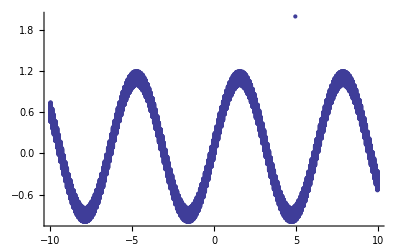

(1.76 secs): Here 2

```mathematica
ans=ListPlot[Flatten[Map[strip,Partition[data,2000]],1]];
Timing˘Print["Here 1"];
Print[ans];
Timing˘Print["Here 2","FrontEndWait"->True]
```

### Case 2 – Data sent to FE using inefficient data structure

Particularly when using low level graphics, it is possible to create structures that do not transfer efficiently over MathLink to the FrontEnd.

```mathematica
data=Table[{Random[],Random[]},{20000}];
```

```mathematica
ans=Graphics[Map[Point[{#}]&,data]];Timing˘Print["Here 1"];Print[ans];Timing˘Print["Here 2","FrontEndWait"->True]
```

(0.10 secs): Here 1

(31.74 secs): Here 2

```mathematica
ans=Graphics[{Point[data]}];Timing˘Print["Here 1"];Print[ans];Timing˘Print["Here 2","FrontEndWait"->True]
```

(0.03 secs): Here 1

(0.53 secs): Here 2

This remarkable performance improvement happens because in the latter case, all the data is stored in a packed array inside one Point construct. The same phenomenon also happens with the Line construct. The packed array transfers to the FrontEnd much more efficiently than 20000 individual Point structures. Interestingly, this difference did not exist prior to version 6.0, because back then graphics were rendered in the kernel.

## Other options for improving performance

There are several other options for improving Mathematica performance, that have not been discussed in this paper. In general it is better to use these after searching for problems of the sort discussed above.

• Use the Compile function – this can give useful gains, but results vary.

• Add more memory to your computer. This will speed up your calculations if they involve a lot of data, and page swapping is occurring. Since there is a limit to the amount of memory that can be used effectively by a 32-bit process (typically 1.8 GB, and always less than 4GB), you should switch to a 64-bit operating system if  you want to use more memory. 64-bit Windows will also run 32-bit code, so this is not as troublesome as it sounds!

• Move a critical part of the code into Java. This is particularly useful for code that can’t easily be made functional. However, the overhead in calling a Java function is high, so it is vital to keep the number of calls to a minimum. Also compile the code as Java code using javac, rather than using successive J/Link calls.

• As of version 8.0, you can call code in C libraries. Unlike Java, these operate in the same process, and the overhead per call is much lower than Java.

• If you have a multi-core processor, you may want to explore parallel computation using multiple kernels. I would say it is best to think of this as a last resort!

## Conclusion

Unless you discover exactly where your program is spending its time, any attempt at optimisation will be a hit and miss process. Although functional programming is an important tool, there are many other reasons why a Mathematica program may be inefficient. Macros allow you to combine readability and efficiency.